# Hazards of Kalman Covariance Updates

Brian Beckman
Dec 2023

## Abstract

Here, we demonstrate Fold over Kalman estimators with five, mathematically equivalent, different forms for the covariance update, each with different numerical hazards.

We use the Wolfram language because it excels at concise expression of mathematical codes. The same ideas can be rendered in any contemporary programming language with minimal support for closures, such as Python, C++, and Java. The approach of the paper is pedagogical with many examples fully worked out.

## Preliminaries

Skip this section unless you are interested in implementation details.

## Definitions

### Abbreviations

obl | observable
obr | observer
obn | observation

### Notations

```mathematica
<<"Notation`"
InfixNotation[⊕,Join];
```

### Utility Functions

gen generates random samples from a covariance matrix. It only honors the diagonal terms, but each individually.

```mathematica
ClearAll[col,row,id,con,zero,len,dim,m,f1,d1,inv,pinv,scalar,groundTruth,randn,gen,dump,pick];
id=IdentityMatrix;
con[c_,m_,n_]:=ConstantArray[c,{m,n}];
con[c_,n_]:=con[c,n,n];
zero[m_,n_]:=con[0.,m,n];
zero[n_]:=con[0.,n];
col[xs_List]:=List/@xs;
col[c_,n_]:=con[c,n,1];
row[xs_List]:=List[xs];
row[c_,n_]:=con[c,1,n];
len=Length;
dim[squareMatrix_List]:=len[squareMatrix⟦1⟧];
m=MatrixForm;
f1=Flatten[#,1]&;
d1=Drop[#,1]&;
inv=Inverse;
pinv=PseudoInverse;
scalar[m1x1_]:=m1x1⟦1,1⟧;
dump[x_]:=(Print[x];x);
groundTruth=({{-3}, {9}, {-4}, {-5}});
pick[n_]:=#⟦n⟧&;
pick[m_,n_]:=#⟦m,n⟧&
randn[σ_:1.0]:=
If[Chop@σ==0.0,0.0,
RandomVariate[NormalDistribution[0.0,σ]]];
(* generate a random sample from a covariance matrix *)
gen[P_]:=
Module[{σs},
σs=Sqrt/@Table[P⟦i,i⟧,{i,dim[P]}];
randn/@σs];
```

TODO: Limitation: scalar observations only.

```mathematica
ClearAll[withTimes,myStyle,stats];
withTimes[times_,obj_]:=MapThread[List,{times,obj}];
myStyle[s_String]:=Style[s,FontFamily->"Candara",FontSize->12];
stats[nym_String,ress_List,σs_List,predictedVariance_:0]:=
Module[{nonNegss,negss},
{negss,nonNegss}=
(* SplitBy doesn't return the required shapes when all the data have the same sign. *)
(* e.g., SplitBy[{-3,-2,-1},Negative] produces {{-3,-2,-1}}, but we need {{-3,-2,-1},{}} *)
(* lest nonNegss not have any value and the destructuring assignment fail with a message. *)
(* SplitBy[Sort[Abs[ress]-σs],#≥0&; *)
(* Some computations produce negative sigma^2 by floating-point error. We do not have a 
principled way to treat those. Just filter them out. *)
With[{pairs=Select[MapThread[List,{Abs[ress],σs}],Im[#⟦2⟧]==0&]},
With[{xs=#1-#2&@@@pairs},
{Select[xs,Negative],Select[xs,#≥0&]}]];
(*Print[<|"ress"->ress,"σs"->σs,"Abs[ress]-σs"->Abs[ress]-σs,
"sortedRess"->Sort[Abs[ress]-σs],
"splittedRess"->SplitBy[Sort[Abs[ress]-σs],#≥0&]|>];*)
Grid[{
{"% "<>nym<>" resids < σ (Expect >= 68)",100.0Length[negss]/Length[ress]},
{nym<>" resids >= σ",1.0Length[nonNegss]},
{nym<>" resids < σ",1.0Length[negss]},
{"average "<>nym<>" resid",Mean[ress]},
{"theoretical std dev",Sqrt@predictedVariance},
{"std dev of "<> nym<>" resids",StandardDeviation[ress]}},
Frame->All]];
```

# Time-Dependent Observation Noise (TDZ)

Here, we finally see serious numerical differences in the mathematically equivalent covariance updates. We begin with a unit test for a new Kalman foldable, a unit test with only one of the updates. We’ll see big differences when we get to the full application on accelerometer calibration.

## KalmanTDZ

### With P← Ξ+Φ.P.Φᵀ - K.D.Kᵀ.

TODO: Limitation: scalar observations only.

```mathematica
ClearAll[kalmanTDZ];
kalmanTDZ[{x_,P_},{Ζ_,Ξ_,Φ_,Γ_,u_,A_,z_}]:=
Module[{x2,P2,D,K},
x2=Φ.x+Γ.u;
P2=Ξ+Φ.P.Φᵀ;
D=Ζ+A.P2.Aᵀ;
K=P2.Aᵀ.inv[D];
(*Print[<|"D"->D,"K"->K,"x"->x,"Ζ"->Ζ,"P"->P,"xn"->x2+K.(z-A.x2),"Pn"->P2-K.D.K^ᵀ|>];*)
{x2+K.(z-A.x2),P2-K.D.Kᵀ}];
```

## Three-State Accelerometer (TIS, TDZ)

Time-Independent State, Time-Dependent Observation Noise, multiple covariance updates.

### sqrt

Sow values if sqrt is attempted on a negative variance.

```mathematica
ClearAll[sqrt];
SetAttributes[sqrt,Listable];
sqrt[z_]:=With[{zc=Identity[z]},
If[zc<0,Sow[<|"z"->z,"zc"->zc|>,"sqrt"];Sqrt[zc],Sqrt[zc]]];
```

### stir

Move labels around in a labels packet. TODO: This can probably be removed, but it make labels packet easier if we apply stir to its result. This is a minor annoyance at best. Don’t bikeshed too much.

```mathematica
ClearAll[stir];
stir[l_]:=(l⟦1;;len@l;;2⟧)⊕(l⟦2;;len@l;;2⟧)
```

### labelsPacket2

Can handle any number of states.

```mathematica
ClearAll[labelsPacket2,labelsPacket2];
labelsPacket2[_,{}]:={};
labelsPacket2[
j:{indNym_String,indUnits_String},{{nym_String,units_String},more___}]:=
Module[{brk,fst},
brk[q_String]:=" / ["<>q<>"]";
fst[q_String]:=nym<>q<>brk@units;
With[{ind=indNym<>brk@indUnits,
res=" Residual",resvs=" Residuals vs. ",
trtvs=" Truth and Estimates vs. "},
{{{fst[res],""},{ind,nym<>resvs<>indNym}},
{{fst[""],""},{ind,nym<>trtvs<>indNym}}}⊕
labelsPacket2[j,{more}]
]];
```

## ExperimentTDZ

TODO: Poorly named; this is a full replacement for experiment.

```mathematica
ClearAll[experimentTDZ];
experimentTDZ[startTime_,endTime_,timeIncrement_,
aPrioriState_,aPrioriCovariance_,fakeFn_,
nStates_Integer:2,truthFns_List:{Identity,Identity},
labelsPacket_List:stir@labelsPacket2[{"Independent Variable","?dim"},{{"State1","?dim"},{"State2","?dim"}}],
statsLabels_List:{"State1","State2"},iterations_Integer:1]:=
Module[{t,timesIter,times,fakes,estss,
trueStates,estimatedStatess,residualStatess,
stddevStatess,theoStateVarss,statsStates,styler},
styler=myStyle/@#&;
timesIter={t,startTime,endTime,timeIncrement};
times=Table[t,Evaluate@timesIter];
trueStates=Table[truthFns⟦n⟧[t],{n,nStates},Evaluate@timesIter];
fakes[]:=Table[fakeFn[timeIncrement,t],Evaluate@timesIter];
estss=Table[
FoldList[kalmanTDZ,{aPrioriState,aPrioriCovariance},fakes[]],
iterations];
(* starts at 2;; to skip the a-priori *)
estimatedStatess=Table[estss⟦;;,2;;,1,n,1⟧,{n,nStates}];
residualStatess=Table[
Identity[trueStates⟦n⟧-#&/@estimatedStatess⟦n⟧],
{n,nStates}];
stddevStatess=Table[sqrt@estss⟦(;;),(2;;),2,n,n⟧,{n,nStates}];
theoStateVarss=Table[Last[estss⟦1⟧]⟦2,n,n⟧,{n,nStates}];
statsStates=Table[
stats[statsLabels⟦n⟧,
f1@residualStatess⟦n⟧,
f1@stddevStatess⟦n⟧,
theoStateVarss⟦n⟧],{n,nStates}];
Grid@{
Table[
ListLinePlot[(withTimes[times,#]&/@residualStatess⟦n⟧)⊕
(withTimes[times,#]&/@stddevStatess⟦n⟧)⊕
(withTimes[times,#]&/@-stddevStatess⟦n⟧),
Frame->True,FrameLabel->styler/@labelsPacket⟦n⟧,
GridLines->All,ImageSize->Medium],{n,nStates}],
Table[
ListLinePlot[{withTimes[times,trueStates⟦n⟧]}⊕
(withTimes[times,#]&/@estimatedStatess⟦n⟧),
Frame->True,FrameLabel->styler/@labelsPacket⟦n+nStates⟧,
GridLines->All,ImageSize->Medium],{n,nStates}],
statsStates}];
```

## ExperimentTDZ with Three-State Accelerometer

### With P ← L.P.Lᵀ+K.Z.Kᵀ, with L=I_3-K.A

```mathematica
ClearAll[kalmanTDZ];
kalmanTDZ[{x_,P_},{Ζ_,A_,z_}]:=
Module[{D,K,L,P1,P3,P4},
D=Ζ+A.P.Aᵀ;
K=P.Aᵀ.inv[D];
L=(id[len[P]]-K.A);
P1=L.P;
P3=L.P.Lᵀ+K.Ζ.Kᵀ;
P4=P-K.D.Kᵀ;
(*Print[<|"P3"->P3|>];*)
Sow[Sqrt[(P1)⟦1,1⟧],"std1"];
Sow[Sqrt[(P1)⟦2,2⟧],"std2"];
Sow[Sqrt[(P1)⟦3,3⟧],"std3"];
{x+K.(z-A.x),P3}];
```

Error in accelerometer is bias + scale * g cos(θ) + drift * (g cos(θ))^2. Three states are bias, scale, and drift. Independent variable is θ.

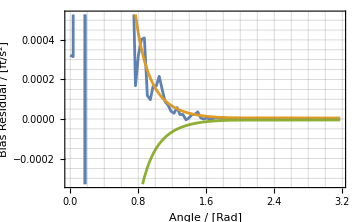
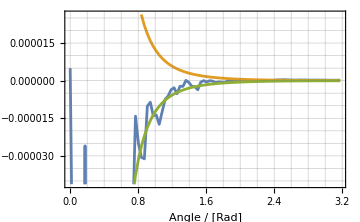
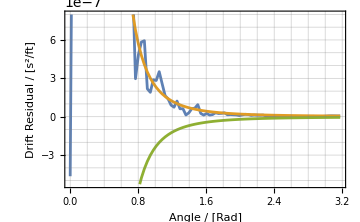
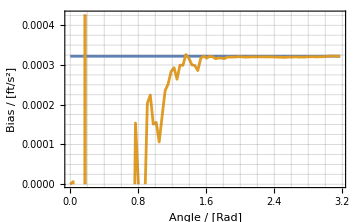
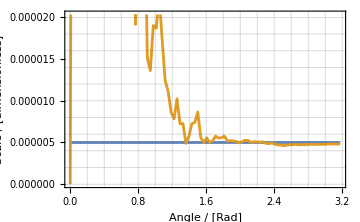
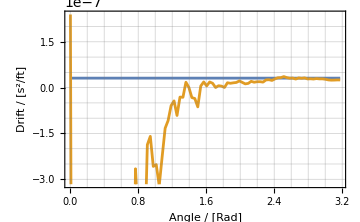
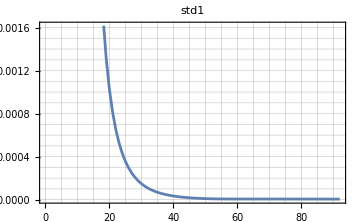
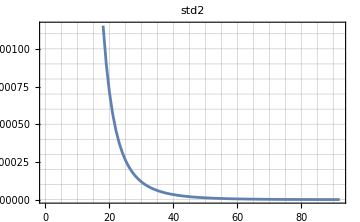
{-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
% Bias resids < σ (Expect >= 68) | 72.8261
Bias resids >= σ | 19.
Bias resids < σ | 67.
average Bias resid | 0.0175505
theoretical std dev | 4.99775×10^-6
std dev of Bias resids | 0.0976125 | % Scale resids < σ (Expect >= 68) | 48.913
Scale resids >= σ | 41.
Scale resids < σ | 45.
average Scale resid | -0.00110364
theoretical std dev | 6.05428×10^-8
std dev of Scale resids | 0.00607685 | % Drift resids < σ (Expect >= 68) | 64.1304
Drift resids >= σ | 27.
Drift resids < σ | 59.
average Drift resid | 0.0000173655
theoretical std dev | 5.63218×10^-9
std dev of Drift resids | 0.0000945739,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{σx=0,σθ=1. 10.^-6,σθtheoretical=1 10^-6,g=32.2,δθ=2.°(*1°/60*),θ0=0.,θ1=180.°},
With[{bias0=10. 10^-6 Abs[g],scale0=5. 10^-6,drift0=1. 10^-6/Abs[g]},
With[{groundTruth={bias0,scale0,drift0},aPrioriState=zero[3,1],aPrioriCovariance=99999999999id[3]},
Module[{Ζ,zees,partials},Ζ[θ_]:=col[{ σθtheoretical^2 g^2(Sin[θ])^2}];
partials[θ_]:=({{1, g Cos[θ], (g Cos[θ])^2}});
SeedRandom[42];
Flatten@{Reap[Reap[Reap[
experimentTDZ[θ0,91δθ,δθ,aPrioriState,aPrioriCovariance,
{dθ,θ}↦
With[{θnoisy=θ+randn[σθ]},
{Ζ[θnoisy], (* observation noise *)
partials[θnoisy], (* observation partials *)
partials[θnoisy].groundTruth+{g Cos[θnoisy]-g Cos[θ]}}], 
3,{θ↦bias0,θ↦scale0,θ↦drift0},
stir@labelsPacket2[{"Angle","Rad"},{{"Bias","ft/s^2"},{"Scale","dimensionless"},{"Drift","s^2/ft"}}],
{"Bias","Scale","Drift"},1],
"std1",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std2",ListLinePlot[zees=Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std3",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&]}]]]]
```

### With P ← L.P, L=I_3-K.A

```mathematica
ClearAll[kalmanTDZ];
kalmanTDZ[{x_,P_},{Ζ_,A_,z_}]:=
Module[{D,K,L,P1,P3,P4},
D=Ζ+A.P.Aᵀ;
K=P.Aᵀ.inv[D];
L=(id[len[P]]-K.A);
P1=L.P;
P3=L.P.Lᵀ+K.Ζ.Kᵀ;
P4=P-K.D.Transpose[K];
(*Print[<|"P3"->P3|>];*)
Sow[Sqrt[(P1)⟦1,1⟧],"std1"];
Sow[Sqrt[(P1)⟦2,2⟧],"std2"];
Sow[Sqrt[(P1)⟦3,3⟧],"std3"];
{x+K.(z-A.x),P1}];
```

Error in accelerometer is bias + scale * g cos(θ) + drift * (g cos(θ))^2. Three states are bias, scale, and drift. Indpendent variable is θ.

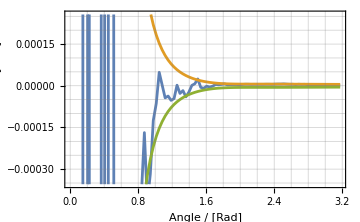
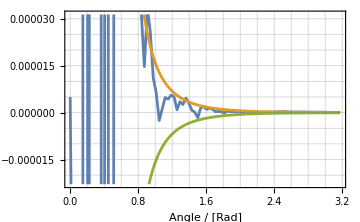
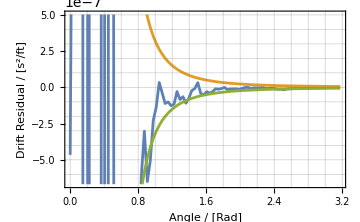
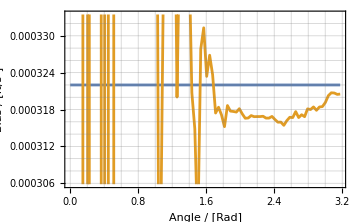
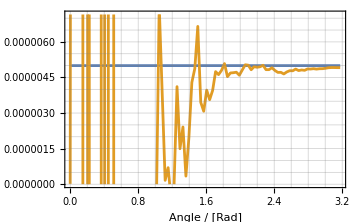
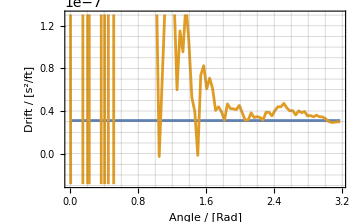
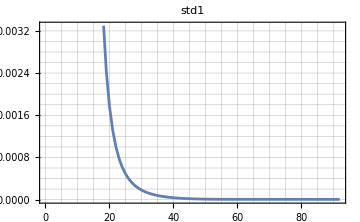
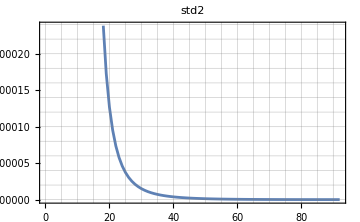
{-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
% Bias resids < σ (Expect >= 68) | 76.087
Bias resids >= σ | 17.
Bias resids < σ | 70.
average Bias resid | -0.00222529
theoretical std dev | 5.06543×10^-6
std dev of Bias resids | 0.0264771 | % Scale resids < σ (Expect >= 68) | 57.6087
Scale resids >= σ | 34.
Scale resids < σ | 53.
average Scale resid | 0.000145862
theoretical std dev | 8.11302×10^-8
std dev of Scale resids | 0.0016693 | % Drift resids < σ (Expect >= 68) | 76.087
Drift resids >= σ | 17.
Drift resids < σ | 70.
average Drift resid | -2.39111×10^-6
theoretical std dev | 6.15038×10^-9
std dev of Drift resids | 0.000026335,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{σx=0,σθ=1. 10.^-6,σθtheoretical=1 10^-6,g=32.2,δθ=2.°(*1°/60*),θ0=0.,θ1=180.°},
With[{bias0=10. 10^-6 Abs[g],scale0=5. 10^-6,drift0=1. 10^-6/Abs[g]},
With[{groundTruth={bias0,scale0,drift0},aPrioriState=zero[3,1],aPrioriCovariance=99999999999id[3]},
Module[{Ζ,zees,partials},Ζ[θ_]:=col[{ σθtheoretical^2 g^2(Sin[θ])^2}];
partials[θ_]:=({{1, g Cos[θ], (g Cos[θ])^2}});
SeedRandom[42];
Flatten@{Reap[Reap[Reap[
experimentTDZ[θ0,91δθ,δθ,aPrioriState,aPrioriCovariance,
{dθ,θ}↦With[{θnoisy=θ+randn[σθ]},
{Ζ[θnoisy], (* observation noise *)
partials[θnoisy], (* observation partials *)
partials[θnoisy].groundTruth+{g Cos[θnoisy]-g Cos[θ]}}], 
3,{θ↦bias0,θ↦scale0,θ↦drift0},
stir@labelsPacket2[{"Angle","Rad"},
{{"Bias","ft/s^2"},{"Scale","dimensionless"},{"Drift","s^2/ft"}}],{"Bias","Scale","Drift"},1],
"std1",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std2",ListLinePlot[zees=Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std3",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&]}]]]]
```

### With P ← P-K.D.Kᵀ

```mathematica
ClearAll[kalmanTDZ];
kalmanTDZ[{x_,P_},{Ζ_,A_,z_}]:=
Module[{D,K,L,P1,P3,P4},
D=Ζ+A.P.Aᵀ;
K=P.Aᵀ.inv[D];
L=(id[len[P]]-K.A);
P1=L.P;
P3=L.P.Lᵀ+K.Ζ.Kᵀ;
P4=P-K.D.Kᵀ;
(*Print[<|"P3"->P3|>];*)
Sow[Sqrt[(P1)⟦1,1⟧],"std1"];
Sow[Sqrt[(P1)⟦2,2⟧],"std2"];
Sow[Sqrt[(P1)⟦3,3⟧],"std3"];
{x+K.(z-A.x),P4(*P2-K.D.K^ᵀ*)}];
```

Error in accelerometer is bias + scale * g cos(θ) + drift * (g cos(θ))^2. Three states are bias, scale, and drift. Indpendent variable is θ.

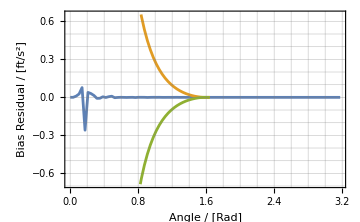
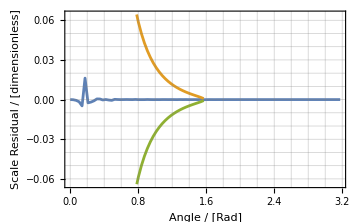
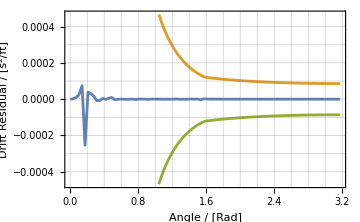
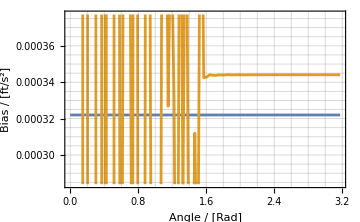
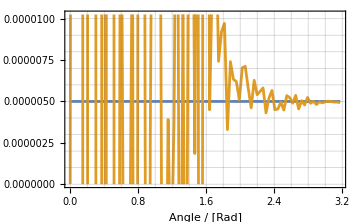
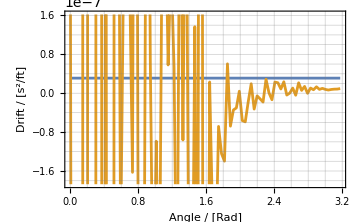
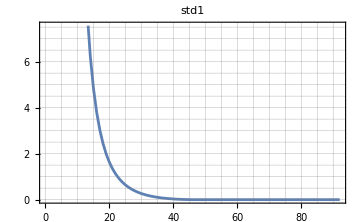
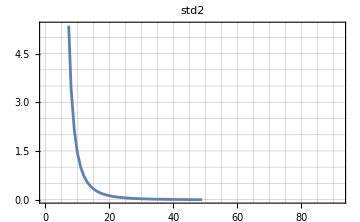
{-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
% Bias resids < σ (Expect >= 68) | 51.087
Bias resids >= σ | 1.
Bias resids < σ | 47.
average Bias resid | -0.000703124
theoretical std dev | 0.+0.0000787154 ⅈ
std dev of Bias resids | 0.0290525 | % Scale resids < σ (Expect >= 68) | 50.
Scale resids >= σ | 0.
Scale resids < σ | 46.
average Scale resid | 0.0000424077
theoretical std dev | 0.+0.00276381 ⅈ
std dev of Scale resids | 0.00181779 | % Drift resids < σ (Expect >= 68) | 100.
Drift resids >= σ | 0.
Drift resids < σ | 92.
average Drift resid | -6.36578×10^-7
theoretical std dev | 0.0000860959
std dev of Drift resids | 0.0000284366,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{σx=0,σθ=1. 10.^-6,σθtheoretical=1 10^-6,g=32.2,δθ=2.°(*1°/60*),θ0=0.,θ1=180.°},
With[{bias0=10. 10^-6 Abs[g],scale0=5. 10^-6,drift0=1. 10^-6/Abs[g]},
With[{groundTruth={bias0,scale0,drift0},aPrioriState=zero[3,1],aPrioriCovariance=99999999999id[3]},
Module[{Ζ,zees,partials},Ζ[θ_]:=col[{ σθtheoretical^2 g^2(Sin[θ])^2}];
partials[θ_]:=({{1, g Cos[θ], (g Cos[θ])^2}});
SeedRandom[42];
Flatten@{Reap[Reap[Reap[
experimentTDZ[θ0,91δθ,δθ,aPrioriState,aPrioriCovariance,
{dθ,θ}↦With[{θnoisy=θ+randn[σθ]},
{Ζ[θnoisy], (* observation noise *)
partials[θnoisy], (* observation partials *)
partials[θnoisy].groundTruth+{g Cos[θnoisy]-g Cos[θ]}}], 
3,{θ↦bias0,θ↦scale0,θ↦drift0},
stir@labelsPacket2[{"Angle","Rad"},
{{"Bias","ft/s^2"},{"Scale","dimensionless"},{"Drift","s^2/ft"}}],{"Bias","Scale","Drift"},1],
"std1",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std2",ListLinePlot[zees=Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&],
"std3",ListLinePlot[Flatten[#2],ImageSize->Medium,Frame->True,GridLines->All,PlotLabel->#1]&]}]]]]
```

## Comparison with Zarchan & Musoff’s Three-State Accelerometer

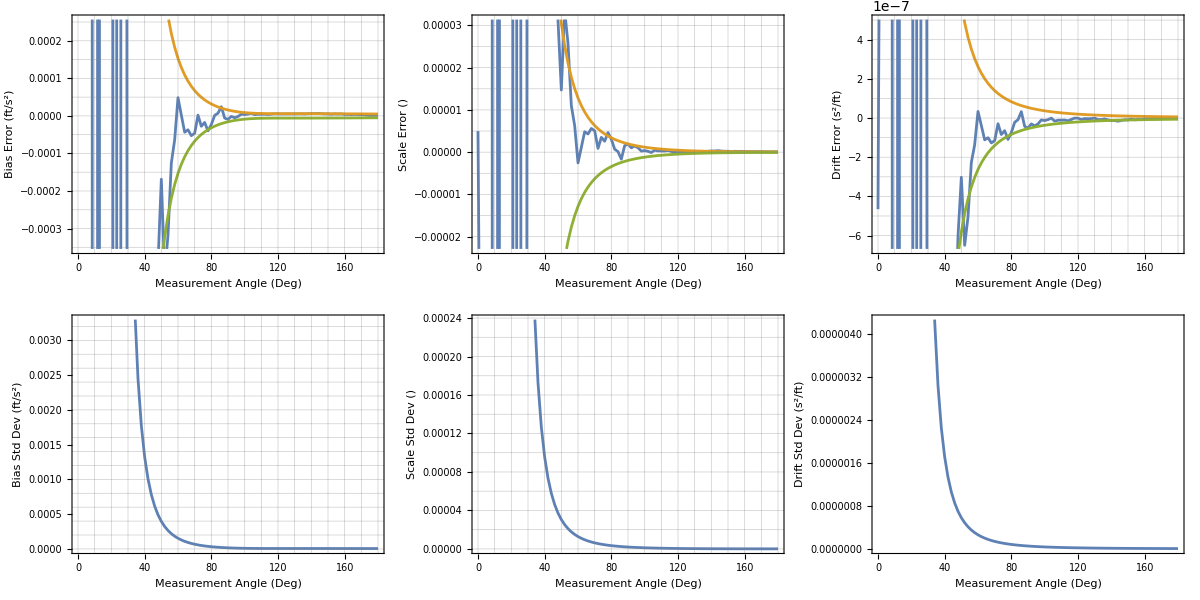
{-Graphics-,{316075.,19611.,19535.2,13771.8,1034.88,0.+177.434 ⅈ,0.+43.0028 ⅈ,0.+12.8091 ⅈ,2.01288,0.+0.0845558 ⅈ,0.+0.0866555 ⅈ,0.0150315,0.00425897,0.00181403,0.000948997,0.000560677,0.00035911,0.000243695,0.000172727,0.000126658,0.0000954451,0.0000735557,0.0000577609,0.0000460858,0.0000372782,0.0000305153,0.0000252417,0.000021073,0.0000177379,0.0000150408,0.0000128384,0.0000110243,9.51793×10^-6,8.25809×10^-6,7.1974×10^-6,6.2989×10^-6,5.53349×10^-6,4.87809×10^-6,4.31415×10^-6,3.82674×10^-6,3.4037×10^-6,3.03512×10^-6,2.7128×10^-6,2.42999×10^-6,2.18105×10^-6,1.96127×10^-6,1.76668×10^-6,1.59396×10^-6,1.44025×10^-6,1.30316×10^-6,1.18062×10^-6,1.07086×10^-6,9.72358×10^-7,8.83811×10^-7,8.04077×10^-7,7.3217×10^-7,6.67231×10^-7,6.0851×10^-7,5.5535×10^-7,5.07176×10^-7,4.63483×10^-7,4.23824×10^-7,3.87807×10^-7,3.55084×10^-7,3.25349×10^-7,2.98328×10^-7,2.73781×10^-7,2.51492×10^-7,2.3127×10^-7,2.12945×10^-7,1.96365×10^-7,1.81394×10^-7,1.67909×10^-7,1.55799×10^-7,1.44964×10^-7,1.35311×10^-7,1.26753×10^-7,1.19209×10^-7,1.12601×10^-7,1.06854×10^-7,1.01895×10^-7,9.76506×10^-8,9.40512×10^-8,9.10279×10^-8,8.85143×10^-8,8.6447×10^-8,8.47668×10^-8,8.34193×10^-8,8.23574×10^-8,8.15527×10^-8,8.11306×10^-8}}

```mathematica
Module[{
order=3,
bias=.00001 * 32.2,
sf=.000005,
xk=.000001/32.2,
sigth=.000001,
g=32.2,
biash=0,
sfh=0,
xkh=0,
signoise=.000001,
s=0,
q=0IdentityMatrix[3],
phi=IdentityMatrix[3],
idnp=IdentityMatrix[3],
p=99999999999IdentityMatrix[3],
ppri,
count=0,
thetdeg,thet,thetnoise,thets,hmat,r,m,k,z,res,sp11,sp22,sp33,sp11p,sp22p,sp33p,biaserr,sferr,xkerr,actnoise,sigr,sigrp,
arraythetdeg,arraybias,arraymhmatt,arrayk11,arrayz,arrayres,arraybiash,arraysf,arraysfh,arrayxk,arrayxkh,arraybiaserr,arraysp11,arraysp11p,arraysferr,arraysp22,arraysp22p,arrayxkerr,arraysp33,arraysp33p,arrayactnoise,arraysigr,arraysigrp},
SeedRandom[42];
{arraythetdeg,arraybias,arraymhmatt,arrayk11,arrayz,arrayres,arraybiash,arraysf,arraysfh,arrayxk,arrayxkh,arraybiaserr,arraysp11,arraysp11p,arraysferr,arraysp22,arraysp22p,arrayxkerr,arraysp33,arraysp33p,arrayactnoise,arraysigr,arraysigrp}=
Reap[For[
thetdeg=0,thetdeg≤180.,thetdeg+=2.,
Sow[thetdeg,"thetdeg"];
Sow[bias,"bias"];
thet=thetdeg*(1.0°)(*/57.3*);
thetnoise=randn@signoise;
thets=thet+thetnoise;
hmat={{1,g Cos[thets],(g Cos[thets])^2}};
r=(g Sin[thets]sigth)^2 IdentityMatrix[1];
m=phi.p.(Transpose[phi])+q;
k=m.(Transpose[hmat]).Inverse[hmat.m.(Transpose[hmat])+r];
Sow[(m.(Transpose[hmat]))⟦1,1⟧,"hmatt"];
Sow[k⟦1,1⟧,"k11"];
ppri=p;
p=(idnp-k.hmat).m;
(*Print[<|"P"->p|>];*)
Sow[z=bias+sf g Cos[thets]+xk (g Cos[thets])^2-g Cos[thet]+g Cos[thets],"z"];
Sow[res=z-biash-sfh g Cos[thets]-xkh(g Cos[thets])^2,"res"];
Sow[biash=biash+k⟦1,1⟧res,"biash"];
Sow[sf,"sf"];
Sow[sfh=sfh+k⟦2,1⟧res,"sfh"];
Sow[xk,"xk"];
Sow[xkh=xkh+k⟦3,1⟧res,"xkh"];
Sow[biaserr=bias-biash,"biaserr"];
Sow[sp11=Sqrt[p⟦1,1⟧],"sp11"];
Sow[sp11p=-sp11,"sp11p"];
Sow[sferr=sf-sfh,"sferr"];
Sow[sp22=Sqrt[p⟦2,2⟧],"sp22"];
Sow[sp22p=-sp22,"sp22p"];
Sow[xkerr=xk-xkh,"xkerr"];
Sow[sp33=Sqrt[p⟦3,3⟧],"sp33"];
Sow[sp33p=-sp33,"sp33p"];
Sow[actnoise=g Cos[thets]-g Cos[thet],"actnoise"];
Sow[sigr=Sqrt[r⟦1,1⟧],"sigr"];
Sow[sigrp=-sigr,"sigrp"];
count=count+1;
]]⟦2⟧;
{Grid[
{{ListLinePlot[{Transpose[{arraythetdeg,arraybiaserr}],Transpose[{arraythetdeg,arraysp11}],Transpose[{arraythetdeg,arraysp11p}]},
ImageSize->Medium,GridLines->All,Frame->True,
FrameLabel->{{"Bias Error (ft/s^2)",""},{"Measurement Angle (Deg)",""}}],
ListLinePlot[{Transpose[{arraythetdeg,arraysferr}],Transpose[{arraythetdeg,arraysp22}],Transpose[{arraythetdeg,arraysp22p}]},
ImageSize->Medium,GridLines->All,Frame->True,
FrameLabel->{{"Scale Error ()",""},{"Measurement Angle (Deg)",""}}],
ListLinePlot[{Transpose[{arraythetdeg,arrayxkerr}],Transpose[{arraythetdeg,arraysp33}],Transpose[{arraythetdeg,arraysp33p}]},
ImageSize->Medium,GridLines->All,Frame->True,
FrameLabel->{{"Drift Error (s^2/ft)",""},{"Measurement Angle (Deg)",""}}]},
{ListLinePlot[{Transpose[{arraythetdeg,arraysp11}]},
ImageSize->Medium,GridLines->All,Frame->True,
FrameLabel->{{"Bias Std Dev (ft/s^2)",""},{"Measurement Angle (Deg)",""}}],
ListLinePlot[{Transpose[{arraythetdeg,arraysp22}]},
ImageSize->Medium,GridLines->All,Frame->True,
FrameLabel->{{"Scale Std Dev ()",""},{"Measurement Angle (Deg)",""}}],
ListLinePlot[{Transpose[{arraythetdeg,arraysp33}]},
ImageSize->Medium,GridLines->All,Frame->True,
FrameLabel->{{"Drift Std Dev (s^2/ft)",""},{"Measurement Angle (Deg)",""}}]
}}],
arraysp22}]
```